```mathematica
IntegerDigits[87109]
```

{8,7,1,0,9}

```mathematica
IntegerDigits[EulerPhi[87109]]
```

{7,9,1,8,0}

```mathematica
ListLinePlot[EulerPhi[x],{x,1,100}]
```

ListLinePlot::nonopt: Options expected (instead of {x, 1, 100}) beyond position 1 in ListLinePlot[EulerPhi[x], {x, 1, 100}]. An option must be a rule or a list of rules.

ListLinePlot[EulerPhi[x],{x,1,100}]

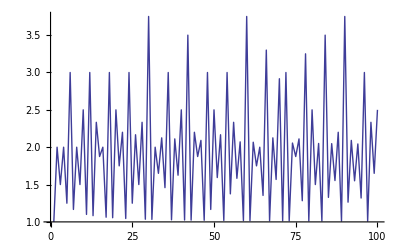

```mathematica
ListLinePlot[Table[x/EulerPhi[x],{x,1,100}]]
```

```mathematica
IsRelevant[x_]:=Sort[IntegerDigits[EulerPhi[x]]]==Sort[IntegerDigits[x]]
```

```mathematica
Timing[Map[Function[n,{n,n/EulerPhi[n]}],Select[Range[(10^6)-100000,10^6],IsRelevant]]]
```

{2.422,{{904032,3139/1008},{906543,100727/61040},{920262,21911/6260},{924075,185/96},{924930,51385/13328},{928638,51591/16576},{932085,20713/8576},{933020,46651/16960},{940212,3731/960},{940417,940417/917440},{942186,157031/44864},{952230,31741/8464},{957248,14957/7478},{957312,277/92},{959607,11847/7160},{964395,107155/55104},{966370,96637/37696},{966753,107417/71064},{972678,162113/46316},{974667,324889/216592},{976384,1907/953},{976482,1391/424},{982566,4199/1152},{984370,492185/195392},{989802,54989/16660},{992416,31013/15506}}}

```mathematica
Timing[Select[Range[2,10^6],IsRelevant]]
```

{34.344,{35683,162619,176481,212101,277621,525121}}

```mathematica
Complement[{1,2,3,4,1},{1}]
```

{2,3,4}

```mathematica
Tally[{1,1,1,2,3}]
```

{{1,3},{2,1},{3,1}}